## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier-visuals/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.17877 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Mar 26, 2020, time: 10:35:59

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/fourier-visuals/bricks-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.17877 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
fticks={{Automatic,Automatic},{{{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}},Automatic}};
fticks={{Automatic,Automatic},{{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}},Automatic}};
nticks={{Automatic,Automatic},{π/2 ints,Automatic}};
nuticks={{Automatic,Automatic},{{{1,0},{10,11},{20,21},{26,25}},Automatic}};
```

```mathematica
𝕔=299792458;
```

```mathematica
isize=ImageSize->4 72;
ipad=ImagePadding->{{Automatic,5},{Automatic,Automatic}};
```

#### functions

```mathematica
Clear[sty];
sty[s_String]:=Style[s,FontFamily->"TimesNewRoman"]
```

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## 2

### set up

#### epilog placement

```mathematica
Λ=1.1;
```

#### frequencies where MoM measured rcs

```mathematica
(* 1°, 2°, 3°, 4°, ... *)
```

```mathematica
Ν=Table[
k
,{k,3,30}];
m=Length[Ν]
```

28

#### maximum expansion order

```mathematica
ω=25;
```

```mathematica
avector=Table[Cos[j θ],{j,0,ω}];
```

```mathematica
masterA=Table[
Simplify[avector/.θ->Ν[[k]]]
,{k,m}];
```

## 3

```mathematica
d=15;
α=0;
```

```mathematica
(* which measurement to grab *)
index=α+181;
λ=Round[𝕔/(ν 1000000)];
rcs=meanRCSᵀ[[index]];
m=Length[rcs];
(* center nose angle *)
σ=RotateLeft[rcs,180];
(* characterize data set *)
μ=Mean[σ];
mx=Max[σ];
mn=Min[σ];
{top,bot}={1.1mx,0.9mn};
subtitle="α = "<>ToString[α]<>"°";
Print[lf,"yaw α = ",α,"°"];
Print["mean rcs = ",μ];
```

yaw α = 0°

mean rcs = 22.429

```mathematica
(* scatter plot of data points *)
z={Ν,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
```

```mathematica
(* define Hilbert space basis functions *)
vector=Take[avector,d+1];
(* grab slice of master matrix *)
A=Take[masterAᵀ,d+1]ᵀ;
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
(* approximation function *)
Clear[f];
f[θ_]=c.vector;
Print["f[θ] = ",f[θ]];
(* approximation vector *)
F=f[n]/.n->Ν;
(* residual error *)
r=σ-F;
R={Ν,r}ᵀ;
(* maximum error *)
emax=Norm[r,∞];
(* total error *)
r2=r.r;
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
(* signal to noise *)
γ=Last[c]/Last[ϵ];
```

f[θ] = 22.7372+1.87958 Cos[θ]+1.68437 Cos[2 θ]+1.19632 Cos[3 θ]+0.0410582 Cos[4 θ]+0.771333 Cos[5 θ]+0.662938 Cos[6 θ]+0.85467 Cos[7 θ]-3.03828 Cos[8 θ]+0.237377 Cos[9 θ]+0.286495 Cos[10 θ]-0.699453 Cos[11 θ]+0.267841 Cos[12 θ]+0.514423 Cos[13 θ]-1.74044 Cos[14 θ]-0.357578 Cos[15 θ]

```mathematica
(* function *)
g001=Plot[f[θ],{θ,3,30},
Frame->True,
PlotRange->Full,
PlotStyle->{Opacity[0.25],Blue}];
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>subtitle,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d,2}],Automatic}},
ipad,isize];
(* amplitudes with errors *)
ebars=Table[
{k-1,Around[c[[k]],ϵ[[k]]]}
,{k,Length[c]}];
gebars=ListPlot[ebars,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[{k,Subscript["a",k]},{k,0,Length[ebars],2}],Automatic}},
PlotLabel->"Amplitudes with errors for d = "<>ToString[d]<>lf<>subtitle,
PlotStyle->Blue,
PlotRange->{{-0.5,d+0.5},Full},
isize,ipad];
(* compare data to fit *)
dsubtitle=subtitle<>", d = "<>ToString[d];
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"<>lf<>dsubtitle],
FrameLabel->{sty["Yaw angle, α"],sty["Mean total RCS, <σ_T>"]},
PlotRange->{bot,top},
isize,ipad];
(* residual error *)
gb=ListPlot[R,
Frame->True,
FrameLabel->{sty["Yaw angle, α"],sty["Residual error"]},
(* PlotRange->Λ{-1,1}, *)
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"<>lf<>dsubtitle],
isize,ipad];
(* group plots *)
gout2=GraphicsRow[{ga,gb},
PlotRange->{bot,top},
ImageSize->12 72];
gout4=GraphicsGrid[{{ga,gb},{gbars,gebars}},
ImageSize->12 72];
```

## show

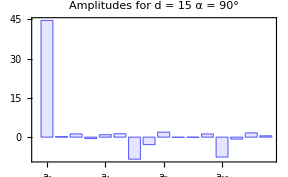

```mathematica
gbars
```

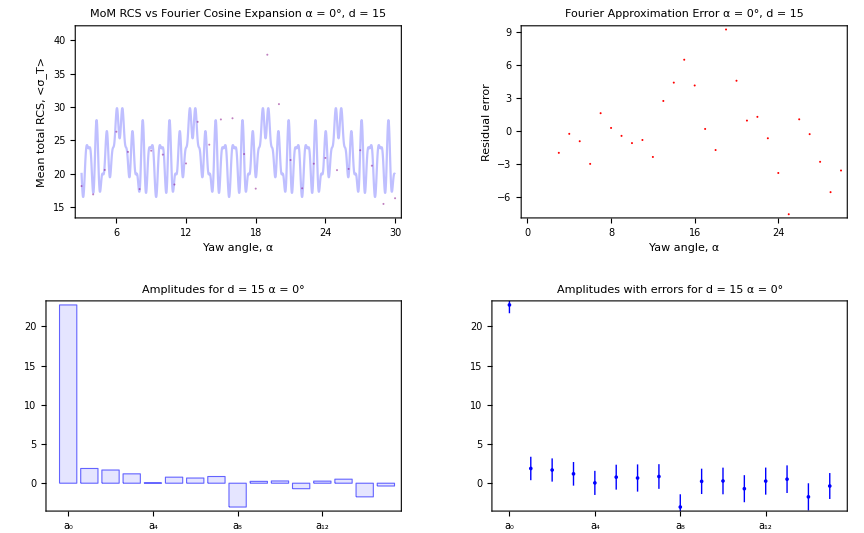

```mathematica
gout4
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```